```mathematica
numbers={a->1.,ν->0.07453,α->0.000002};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом\Diploma_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-4;;NumPlace[x]+4]],AbsFourier[x][[NumPlace[x]-4;;NumPlace[x]+4]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;Length[x]/2+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
```

N = 100

```mathematica
sig100=Table[(0.53836-0.46164Cos[(2Pi*k)/99])a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,100}];
```

0.07

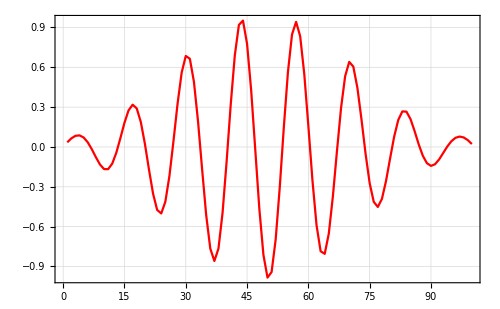

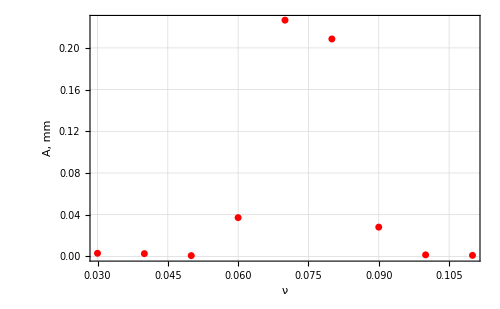

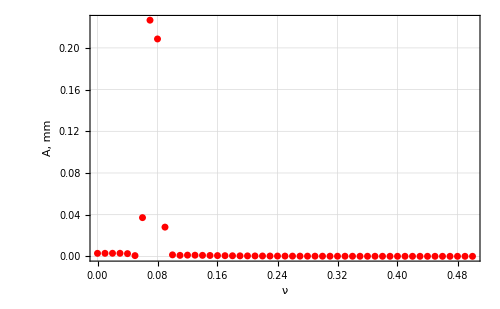

```mathematica
Freq100 =Freq[sig100]
Image100=ListLinePlot[sig100]
Fourier100=TruePlot[sig100]
FourierFull100=FullPlot[sig100]
```

N = 500

```mathematica
sig500=Table[(0.53836-0.46164Cos[(2Pi*k)/499])a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,500}];
```

0.074

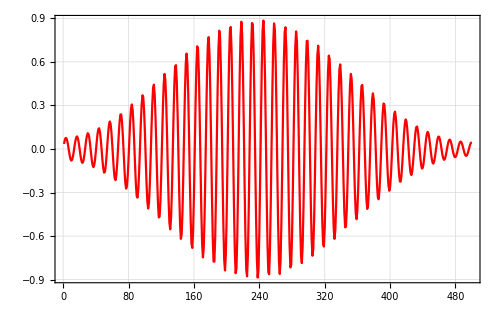

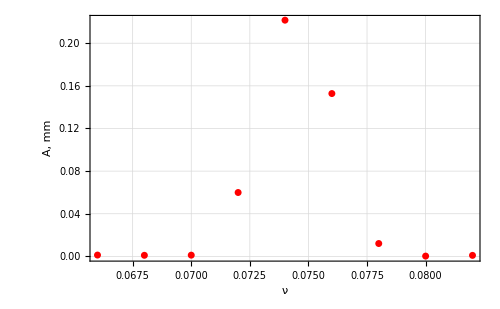

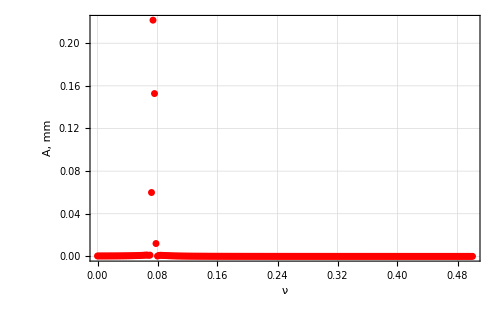

```mathematica
Freq500 =Freq[sig500]
Image500=ListLinePlot[sig500]
Fourier500=TruePlot[sig500]
FourierFull500=FullPlot[sig500]
```

N = 1000

0.075

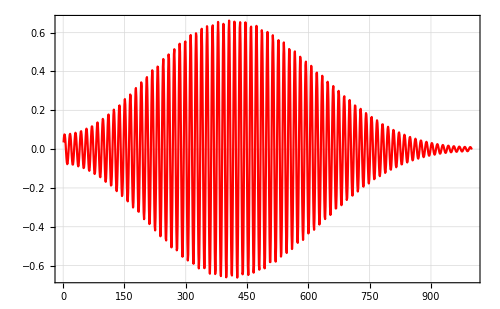

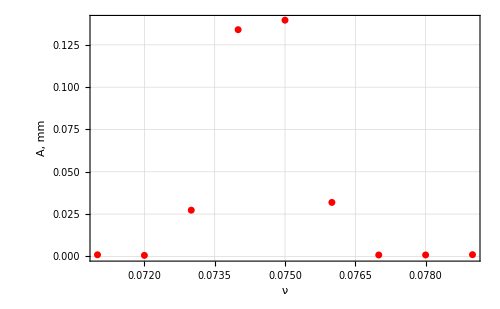

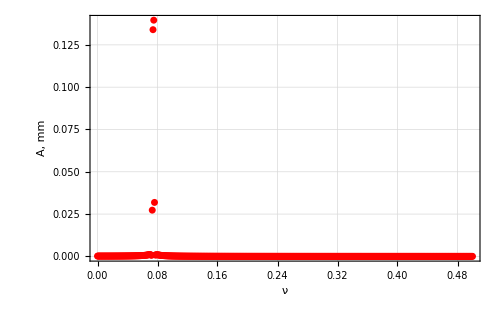

```mathematica
sig1000=Table[(0.53836-0.46164Cos[(2Pi*k)/999])a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,1000}];
Freq1000 =Freq[sig1000]
Image1000=ListLinePlot[sig1000]
Fourier1000=TruePlot[sig1000]
FourierFull1000=FullPlot[sig1000]
```

N = 1500

0.0746667

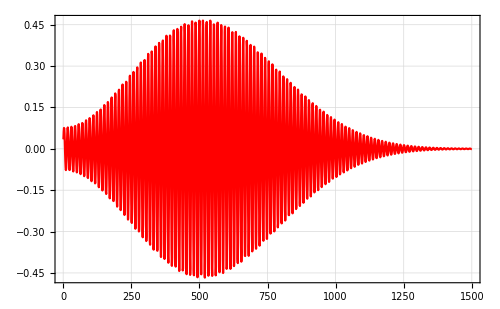

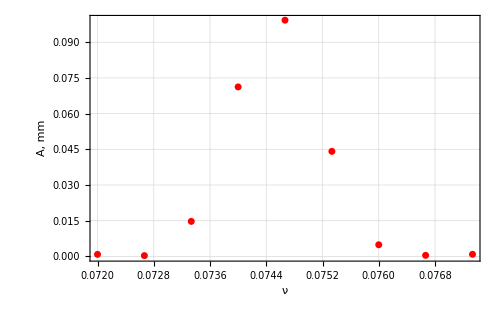

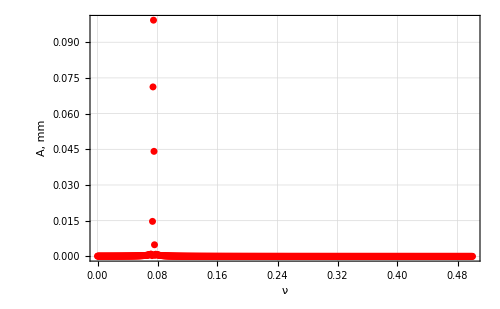

Hamming1500.png

```mathematica
sig1500=Table[(0.53836-0.46164Cos[(2Pi*k)/1499])a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,1500}];
Freq1500 =Freq[sig1500]
Image1500=ListLinePlot[sig1500]
Fourier1500=TruePlot[sig1500]
FourierFull1500=FullPlot[sig1500]
Export["Hamming1500.png",Fourier1500]
```

N = 3000

0.0746667

-Graphics-

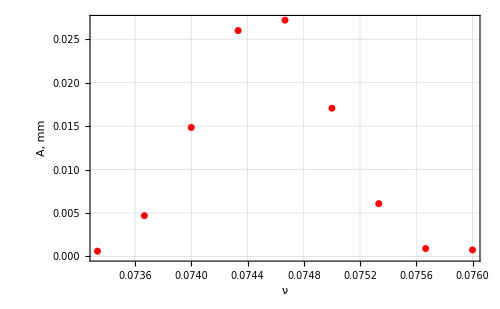

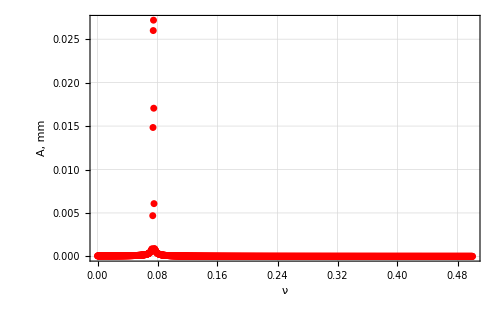

```mathematica
sig3000=Table[(0.53836-0.46164Cos[(2Pi*k)/2999])a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,3000}];
Freq3000 =Freq[sig3000]
Image3000=ListLinePlot[sig1000]
Fourier3000=TruePlot[sig3000]
FourierFull3000=FullPlot[sig3000]
```

```mathematica
depen =Transpose[{{100,500,1000,1500,3000},{Freq100, Freq500,Freq1000,Freq1500,Freq3000}-ν}/.numbers];
```

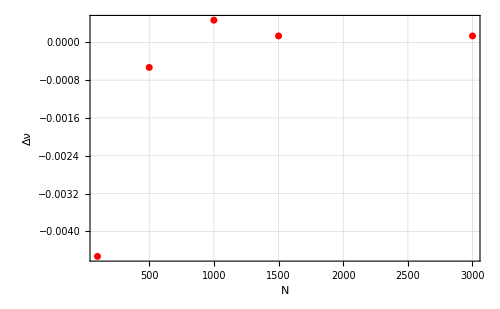

```mathematica
DeltaHamming=ListPlot[depen,Axes->True,FrameLabel->{"N","Δν"}]
```

```mathematica
Export["DeltaHamming.png",DeltaHamming]
```

DeltaHamming.png

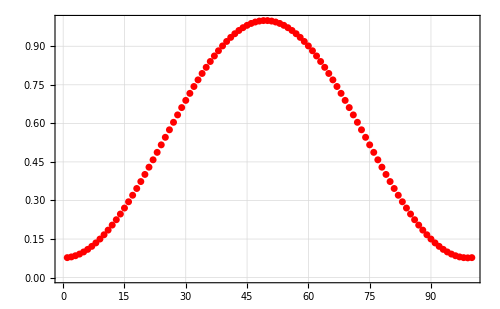

```mathematica
Hamming=Table[(0.53836-0.46164Cos[(2Pi*k)/99]),{k,1,100}];
HammingPlot=ListPlot[Hamming]
```

```mathematica
Export["Hamming_Window.png",HammingPlot]
```

Hamming_Window.png